### Interlayer hopping at Γ

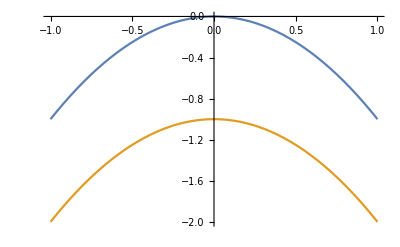

```mathematica
(* If you have two parabolic valence bands of the two layers at different energy, the dispersion looks like this: *)
Plot[{-k^2,-k^2-1},{k,-1,1}]
```

```mathematica
(* Imagine you have an interlayer coupling of the form -a*(1-k^2) where a is some tuning parameter *)
(* Define the bilayer Hamiltonian *)
BilayerHamiltonian={{-k^2,-a*(1-k^2)},{-a*(1-k^2),-k^2-1}};
(* Show it *)
BilayerHamiltonian//TraditionalForm
(* Calculate the eigenvalues *)
Eigenvalues[BilayerHamiltonian]
```

(-k^2 | -a (1-k^2)
-a (1-k^2) | -k^2-1)

{1/2 (-1-2 k^2-√(1+4 a^2-8 a^2 k^2+4 a^2 k^4)),1/2 (-1-2 k^2+√(1+4 a^2-8 a^2 k^2+4 a^2 k^4))}

```mathematica
(* Visualize the change in dispersion when a becomes nonzero *)
Manipulate[
Plot[{1/2 (-1-2 k^2-√(1+4 a^2-8 a^2 k^2+4 a^2 k^4)),1/2 (-1-2 k^2+√(1+4 a^2-8 a^2 k^2+4 a^2 k^4))},{k,-1,1}],{a,0,1}]
```